# Уравнения математической физики

## Лектор:Корзюк Виктор Иванович, академик

## Преподаватель: Кулешов Александр Аркадьевич, аудитория 407

Студентка 9 группы 4 курса Харитонова Вероника Ренальдовна

# Классификация ДУ в частных производных с переменными коэффициентами.

В следующих задачах на плоскости переменных x, y необходимо выделить подмножество, где уравнения имеют эллиптический, гиперболический и параболический, а также изобразить эти множества графически, используя графические возможности системы Mathematica.

Задача1.

(∂^2 U)/(∂x^2) -x (∂^2 U)/(∂y^2) = 0

Определение типа уравнения не зависит от того, является ли коэффициенты переменными величинами или нет. У нас уравнение 2-го порядка с двумя переменными. Тип такого уравнения определяется вычмслением определителя матрицы старших коэффициентов.

```mathematica
A = ({{1, 0}, {0, -x}});
Det[A]
```

-x

Уравнение эллиптического типа, если -x>0 , гиперболического, если -x < 0, параболического, если лежат на прямой y.

Задание. Изобразить на плоскости переменные x, y - области, задаваемые неравенствами -x > 0, -x < 0.

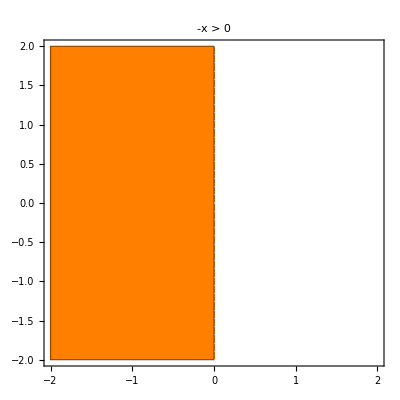

```mathematica
RegionPlot[-x > 0, {x, -2,2}, {y,-2,2}, PlotStyle->Orange, PlotLabel->"-x > 0"]
```

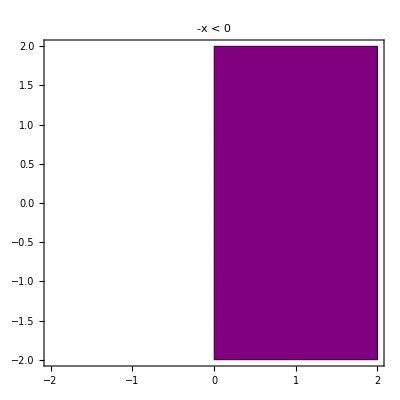

```mathematica
RegionPlot[-x < 0, {x, -2,2}, {y,-2,2}, PlotStyle->Purple, PlotLabel->"-x < 0"]
```